## sigma

```mathematica
Clear[sig,s,μ,B,v0];
sig[B_,μ_,v0_,βintra11_,{s_,sm_}]:=Block[{e=1,sol0,sol2,matr,bc1,bc2,θ,τ1,τ2,kf1,ϕ=0,kf2,f1,f2,vvec1,vvec2,vmm1,vmm2,vdotk1,vdotk2,conteq,h1,h2,λ1,a1,b1,c1,d1,g1,λ2,a2,b2,c2,d2,g2,cost,θp,Dphase1,Dphase2,vz1,vz2,cs,zero1,zero2,ct1,ct2,ctsq1,ctsq2,hzero1,hzero2,hct1,hct2,hctsq1,hctsq2,hctcube1,hctcube2,ctcube1,ctcube2,ctfive1,ctfive2,ctsix1,ctsix2,ctquad1 ,ctquad2,colvec,mat,sol,sol1,Λ1,Λ2,s1,s2,int1,int2},
kf1[θ_]=(μ+√(μ^2-2 B e sm v0^2 Cos[θ]))/(2 v0);
bc1[θ_]=-s/( kf1[θ])^2{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase1[θ_]=1 +e {0,0,B}.bc1[θ] (*-Graphics-*);
vvec1[θ_]=s v0{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm1[θ_]=(-  sm B e v0)/( kf1[θ])^2{Cos[ϕ] Sin[2θ],Sin[2θ] Sin[ϕ], Cos[2 θ]};
vdotk1[θ_]=v0 (s-(B e sm Cos[θ])/kf1[θ]^2) kf1[θ];
h1[θ_]=1/Dphase1[θ]( s v0 Cos[θ]-(B e sm v0 Cos[2 θ])/kf1[θ]^2+ e B(bc1[θ].(vvec1[θ]+vmm1[θ])) );
(*****************)

τ1[θ_]=(βintra11  )^-1;
(****************************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];

ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ctsq1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
ctcube1=Quiet[NIntegrate [f1[θp] Cos[θp]^3,{θp,0,π}]];
ctquad1 =Quiet[NIntegrate [f1[θp] Cos[θp]^4,{θp,0,π}]];
ctfive1=Quiet[NIntegrate [f1[θp] Cos[θp]^5,{θp,0,π}]];
ctsix1=Quiet[NIntegrate [f1[θp] Cos[θp]^6,{θp,0,π}]];
hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];
hctsq1=Quiet[NIntegrate [f1[θp]h1[θp] Cos[θp]^2,{θp,0,π}]];
hctcube1=Quiet[NIntegrate [f1[θp]h1[θp] Cos[θp]^3,{θp,0,π}]];
colvec=({{(-3 hctsq1+5 hzero1 )βintra11}, {(17 hct1-27 hctcube1) βintra11}, {9 hctsq1 βintra11-3 hzero1 βintra11}, {9 (-3 hct1+5 hctcube1) βintra11}});
mat=({{1+3 ctsq1 βintra11-5 zero1 βintra11, -5 ct1 βintra11+3 ctcube1 βintra11, (3 ctquad1-5 ctsq1) βintra11, -5 ctcube1 βintra11+3 ctfive1 βintra11}, {-17 ct1 βintra11+27 ctcube1 βintra11, 1+27 ctquad1 βintra11-17 ctsq1 βintra11, -17 ctcube1 βintra11+27 ctfive1 βintra11, -17 ctquad1 βintra11+27 ctsix1 βintra11}, {3 (-3 ctsq1+zero1) βintra11, 3 (ct1-3 ctcube1) βintra11, 1-9 ctquad1 βintra11+3 ctsq1 βintra11, 3 (ctcube1-3 ctfive1) βintra11}, {9 (3 ct1-5 ctcube1) βintra11, 9 (-5 ctquad1+3 ctsq1) βintra11, 9 (3 ctcube1-5 ctfive1) βintra11, 1+27 ctquad1 βintra11-45 ctsix1 βintra11}});
matr=mat.{λ1,a1,b1,c1};(* λ1 - h1+  a1 ct+b1 ct^2+c1  ct^3 *)
cs=(λ1 zero1-hzero1+a1 ct1+b1 ctsq1+c1 ctcube1);
sol2=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[4]]+colvec[[4]]==0,cs==0},{λ1,a1,b1,c1}],1];

sol=sol2;
Λ1[θ_]=(λ1-h1[θ]+a1 Cos[θ]+b1 Cos[θ]^2+c1  Cos[θ]^3)/.sol;
int1[θ_]=-f1[θ]h1[θ]Λ1[θ];
s1=NIntegrate[int1[θ],{θ,0,π}];
{B,s1(*,MatrixRank[mat//Chop],sol0,sol1,MatrixForm[{λ1,a1,b1,c1}/.sol2]*)}
];
mu=10.0^-1;v0val= 6 10^-4;in=1;bval=1;
sig[bval,mu,v0val,in,{3/2,3/4}]//Quiet
sig[bval,mu,v0val,in,{1/2,7/4}]//Quiet
```

{1,-1.0125×10^-6}

{1,-1.125×10^-7}

```mathematica
Clear[sigm0,s,μ,B,v0];
sigm0[B_,μ_,v0_,βintra11_,s_]:=Block[{e=1,sm=0,sol0,sol2,matr,bc1,bc2,θ,τ1,τ2,kf1,ϕ=0,kf2,f1,f2,vvec1,vvec2,vmm1,vmm2,vdotk1,vdotk2,conteq,h1,h2,λ1,a1,b1,c1,d1,g1,λ2,a2,b2,c2,d2,g2,cost,θp,Dphase1,Dphase2,vz1,vz2,cs,zero1,zero2,ct1,ct2,ctsq1,ctsq2,hzero1,hzero2,hct1,hct2,hctsq1,hctsq2,hctcube1,hctcube2,ctcube1,ctcube2,ctfive1,ctfive2,ctsix1,ctsix2,ctquad1 ,ctquad2,colvec,mat,sol,sol1,Λ1,Λ2,s1,s2,int1,int2},
kf1[θ_]=μ/v0;
bc1[θ_]=-s/( kf1[θ])^2{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase1[θ_]=1 +e {0,0,B}.bc1[θ] (*-Graphics-*);
vvec1[θ_]=s v0{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm1[θ_]=0{Cos[ϕ] Sin[2θ],Sin[2θ] Sin[ϕ], Cos[2 θ]};
vdotk1[θ_]=v0  s  kf1[θ];
h1[θ_]=1/Dphase1[θ]( s v0 Cos[θ]+ e B(bc1[θ].(vvec1[θ]+vmm1[θ])) );
(*****************)

τ1[θ_]=(βintra11  )^-1;
(****************************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];

ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ctsq1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
ctcube1=Quiet[NIntegrate [f1[θp] Cos[θp]^3,{θp,0,π}]];
ctquad1 =Quiet[NIntegrate [f1[θp] Cos[θp]^4,{θp,0,π}]];
ctfive1=Quiet[NIntegrate [f1[θp] Cos[θp]^5,{θp,0,π}]];
ctsix1=Quiet[NIntegrate [f1[θp] Cos[θp]^6,{θp,0,π}]];
hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];
hctsq1=Quiet[NIntegrate [f1[θp]h1[θp] Cos[θp]^2,{θp,0,π}]];
hctcube1=Quiet[NIntegrate [f1[θp]h1[θp] Cos[θp]^3,{θp,0,π}]];
colvec=({{(-3 hctsq1+5 hzero1 )βintra11}, {(17 hct1-27 hctcube1) βintra11}, {9 hctsq1 βintra11-3 hzero1 βintra11}, {9 (-3 hct1+5 hctcube1) βintra11}});
mat=({{1+3 ctsq1 βintra11-5 zero1 βintra11, -5 ct1 βintra11+3 ctcube1 βintra11, (3 ctquad1-5 ctsq1) βintra11, -5 ctcube1 βintra11+3 ctfive1 βintra11}, {-17 ct1 βintra11+27 ctcube1 βintra11, 1+27 ctquad1 βintra11-17 ctsq1 βintra11, -17 ctcube1 βintra11+27 ctfive1 βintra11, -17 ctquad1 βintra11+27 ctsix1 βintra11}, {3 (-3 ctsq1+zero1) βintra11, 3 (ct1-3 ctcube1) βintra11, 1-9 ctquad1 βintra11+3 ctsq1 βintra11, 3 (ctcube1-3 ctfive1) βintra11}, {9 (3 ct1-5 ctcube1) βintra11, 9 (-5 ctquad1+3 ctsq1) βintra11, 9 (3 ctcube1-5 ctfive1) βintra11, 1+27 ctquad1 βintra11-45 ctsix1 βintra11}});
matr=mat.{λ1,a1,b1,c1};(* λ1 - h1+  a1 ct+b1 ct^2+c1  ct^3 *)
cs=(λ1 zero1-hzero1+a1 ct1+b1 ctsq1+c1 ctcube1);

sol2=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[4]]+colvec[[4]]==0,cs==0},{λ1,a1,b1,c1}],1];

sol=sol2;
Λ1[θ_]=(λ1-h1[θ]+a1 Cos[θ]+b1 Cos[θ]^2+c1  Cos[θ]^3)/.sol;
int1[θ_]=-f1[θ]h1[θ]Λ1[θ];
s1=NIntegrate[int1[θ],{θ,0,π}];
{B,s1(*,MatrixRank[mat//Chop],sol0,sol1,MatrixForm[{λ1,a1,b1,c1}/.sol2]*)}
];
mu=10.0^-1;v0val= 6 10^-4;in=1;bval=1;
sigm0[bval,mu,v0val,in,3/2]//Quiet
sigm0[bval,mu,v0val,in,1/2]//Quiet
```

{1,-1.0125×10^-6}

{1,-1.125×10^-7}

## sigma at B=0

```mathematica
Clear[sig10,s,μ,B,v0];
sig0[μ_,v0_,βintra11_,s_]:=Block[{e=1,B=0,sm=0,sol0,sol2,matr,bc1,bc2,θ,τ1,τ2,kf1,ϕ=0,kf2,f1,f2,vvec1,vvec2,vmm1,vmm2,vdotk1,vdotk2,conteq,h1,h2,λ1,a1,b1,c1,d1,g1,λ2,a2,b2,c2,d2,g2,cost,θp,Dphase1,Dphase2,vz1,vz2,cs,zero1,zero2,ct1,ct2,ctsq1,ctsq2,hzero1,hzero2,hct1,hct2,hctsq1,hctsq2,hctcube1,hctcube2,ctcube1,ctcube2,ctfive1,ctfive2,ctsix1,ctsix2,ctquad1 ,ctquad2,colvec,mat,sol,sol1,Λ1,Λ2,s1,s2,int1,int2},
(* band 1 *)
s=1/2;
kf1[θ_]=μ/v0;
bc1[θ_]=-s/( kf1[θ])^2{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase1[θ_]=1 ;
vvec1[θ_]=s v0{ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm1[θ_]={0,0,0};
vdotk1[θ_]=v0 s kf1[θ];
h1[θ_]=1/Dphase1[θ]( s v0 Cos[θ]);
(*****************)

τ1[θ_]=(βintra11  )^-1;
(****************************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];

ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ctsq1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
ctcube1=Quiet[NIntegrate [f1[θp] Cos[θp]^3,{θp,0,π}]];
ctquad1 =Quiet[NIntegrate [f1[θp] Cos[θp]^4,{θp,0,π}]];
ctfive1=Quiet[NIntegrate [f1[θp] Cos[θp]^5,{θp,0,π}]];
ctsix1=Quiet[NIntegrate [f1[θp] Cos[θp]^6,{θp,0,π}]];
hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];
hctsq1=Quiet[NIntegrate [f1[θp]h1[θp] Cos[θp]^2,{θp,0,π}]];
hctcube1=Quiet[NIntegrate [f1[θp]h1[θp] Cos[θp]^3,{θp,0,π}]];
colvec=({{(-3 hctsq1+5 hzero1 )βintra11}, {(17 hct1-27 hctcube1) βintra11}, {9 hctsq1 βintra11-3 hzero1 βintra11}, {9 (-3 hct1+5 hctcube1) βintra11}});
mat=({{1+3 ctsq1 βintra11-5 zero1 βintra11, -5 ct1 βintra11+3 ctcube1 βintra11, (3 ctquad1-5 ctsq1) βintra11, -5 ctcube1 βintra11+3 ctfive1 βintra11}, {-17 ct1 βintra11+27 ctcube1 βintra11, 1+27 ctquad1 βintra11-17 ctsq1 βintra11, -17 ctcube1 βintra11+27 ctfive1 βintra11, -17 ctquad1 βintra11+27 ctsix1 βintra11}, {3 (-3 ctsq1+zero1) βintra11, 3 (ct1-3 ctcube1) βintra11, 1-9 ctquad1 βintra11+3 ctsq1 βintra11, 3 (ctcube1-3 ctfive1) βintra11}, {9 (3 ct1-5 ctcube1) βintra11, 9 (-5 ctquad1+3 ctsq1) βintra11, 9 (3 ctcube1-5 ctfive1) βintra11, 1+27 ctquad1 βintra11-45 ctsix1 βintra11}});
matr=mat.{λ1,a1,b1,c1};(* λ1 - h1+  a1 ct+b1 ct^2+c1  ct^3 *)
cs=(λ1 zero1-hzero1+a1 ct1+b1 ctsq1+c1 ctcube1);

sol2=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[2]]+colvec[[2]]==0,matr[[4]]+colvec[[4]]==0,cs==0},{λ1,a1,b1,c1}],1];

sol=sol2;
Λ1[θ_]=(λ1-h1[θ]+a1 Cos[θ]+b1 Cos[θ]^2+c1  Cos[θ]^3)/.sol;
int1[θ_]=-f1[θ]h1[θ]Λ1[θ];
s1=NIntegrate[int1[θ],{θ,0,π}];
{B,s1(*,MatrixRank[mat//Chop],sol0,sol1,MatrixForm[{λ1,a1,b1,c1}/.sol2]*)}
];
mu=10.0^-1;v0val= 6 10^-4;in=1;bval=1;
sig0[mu,v0val,in,3/2]//Quiet
sig0[mu,v0val,in,1/2]//Quiet
```

{0,-1.0125×10^-6}

{0,-1.125×10^-7}

## data

{0,-0.0000112502}

{0,-0.000101256}

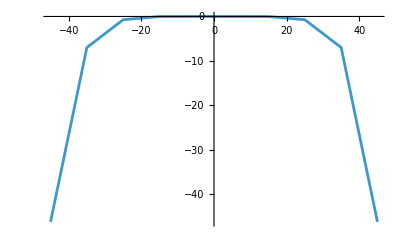

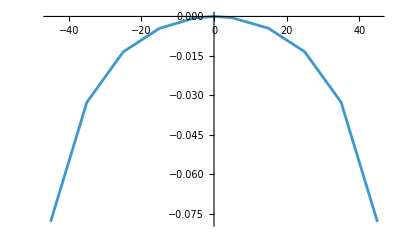

```mathematica
mu=10.0^-1;v0val= 6 10^-3;in=1;
x1=Quiet[sig0[mu,v0val,in,1/2]]
x2=Quiet[sig0[mu,v0val,in,3/2]]
list1=Sort[Join[{x1},Table[Quiet[sig[B,mu,v0val,in,{1/2,7/4}]],{B,-45,45,10}]]];
list2=Sort[Join[{x2},Table[Quiet[sig[B,mu,v0val,in,{3/2,3/4}]],{B,-45,45,10}]]];
len=Length[list1];
dat01=Table[{list1[[i,1]],(Re[list1[[i,2]]]/x1[[2]] -1)10^0},{i,1,len}];
dat02=Table[{list2[[i,1]],(Re[list2[[i,2]]]/x2[[2]]-1)10^0},{i,1,len}];
ListLinePlot[dat01]
ListLinePlot[dat02]
```

{0,-0.0000112502}

{0,-0.000101256}

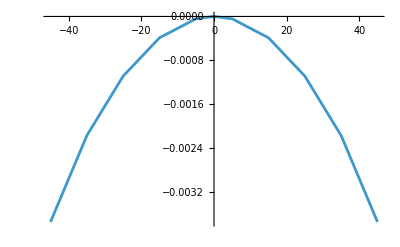

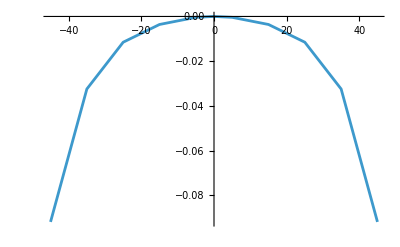

```mathematica
mu=10.0^-1;v0val= 6 10^-3;in=1;
x1=Quiet[sig0[mu,v0val,in,1/2]]
x2=Quiet[sig0[mu,v0val,in,3/2]]
list1=Sort[Join[{x1},Table[Quiet[sigm0[B,mu,v0val,in,1/2]],{B,-45,45,10}]]];
list2=Sort[Join[{x2},Table[Quiet[sigm0[B,mu,v0val,in,3/2]],{B,-45,45,10}]]];
len=Length[list1];
dat11=Table[{list1[[i,1]],(Re[list1[[i,2]]]/x1[[2]]-1)10^0},{i,1,len}];
dat12=Table[{list2[[i,1]],(Re[list2[[i,2]]]/x2[[2]]-1)10^0},{i,1,len}];
ListLinePlot[dat11]
ListLinePlot[dat12]
```

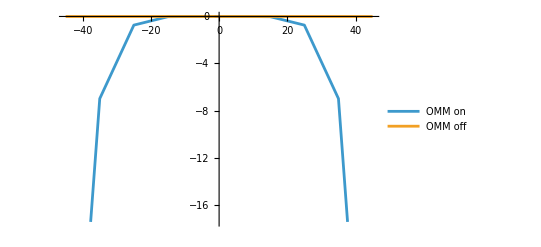

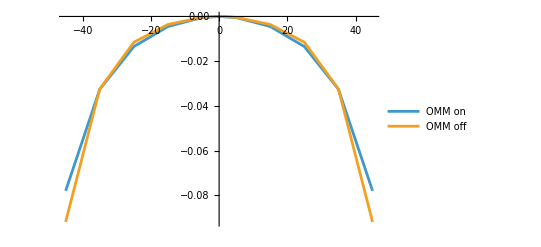

```mathematica
ListLinePlot[{dat01,dat11},PlotLegends->{"OMM on","OMM off"}]
ListLinePlot[{dat02,dat12},PlotLegends->{"OMM on","OMM off"}]
```